```mathematica
CalculateInfected[colors_List]:=
#⟦1⟧&/@Select[
Transpose@{Range[Length[colors]], colors}, 
#⟦2⟧==0&]
```

```mathematica
DrawGraph[G_Graph,colors_List]:=
SetProperty[{G,CalculateInfected[colors]},VertexStyle->Black]
```

```mathematica
CheckNeighbours[G_Graph,Z_List,colors_List, u_]:=
Module[{
neigh=Complement[AdjacencyList[G,u],Z]
},
If[Length[neigh]==1,First[neigh],False]
]
```

```mathematica
SimulateZF[G_Graph,colors_List]:=
Module[{
Z=CalculateInfected[colors],
n=Length[VertexList[G]],
newColors=colors,
Zprev={},
v,
newInf={},
step=1,
allColors={},
},
While[Sort[Z]≠Sort[Zprev],
AppendTo[allColors,newColors];
Table[
v=CheckNeighbours[G,Z,newColors,u];
If[NumberQ[v],newColors⟦v⟧=0; AppendTo[newInf,v]]
,{u,Z}];
Zprev=Z;
Z=Z~Join~newInf; newInf={};
step=step+1;
(* Print[DrawGraph[G,newColors]]*)
];
{step,allColors}
]
```

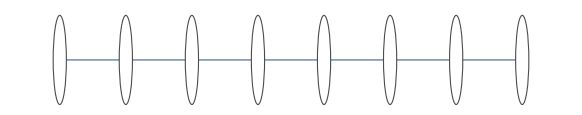

```mathematica
n = 8;
G =PathGraph[Range[n],VertexLabels->"Name", VertexStyle->White, VertexSize->Medium]
(* n = Length[VertexList[G]]; *)
```

```mathematica
colors={0,1,1,1,1,1,1,1};
results=SimulateZF[G, colors];
```

```mathematica
Manipulate[DrawGraph[G, results⟦2⟧⟦a⟧],{a,1,results⟦1⟧-1,1}]
```

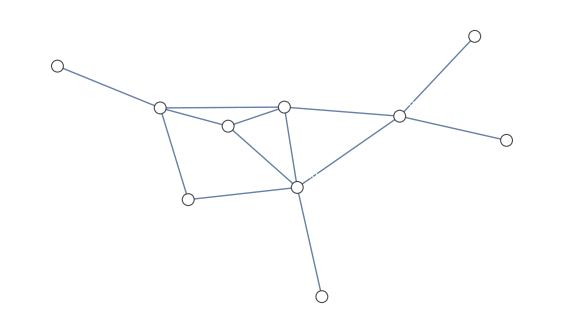

```mathematica
G1=Graph[List[1,2,3,4,5,6,7,8,9,10],List[Null,SparseArray[Automatic,List[10,10],0,List[1,List[List[0,3,5,6,7,8,12,16,17,21,26],List[List[7],List[9],List[10],List[7],List[10],List[7],List[6],List[6],List[4],List[5],List[9],List[10],List[1],List[2],List[3],List[9],List[10],List[1],List[6],List[7],List[10],List[1],List[2],List[6],List[8],List[9]]],Pattern]]],List[Rule[VertexLabels,List["Name"]],Rule[VertexSize,List[Medium]],Rule[VertexStyle,List[GrayLevel[1]]]]]
```

```mathematica
colors1={1,0,0,0,0,0,1,1,1,1};
results1=SimulateZF[G1,colors1];
Manipulate[DrawGraph[G1, results1⟦2⟧⟦a⟧],{a,1,results1⟦1⟧-1,1}]
```